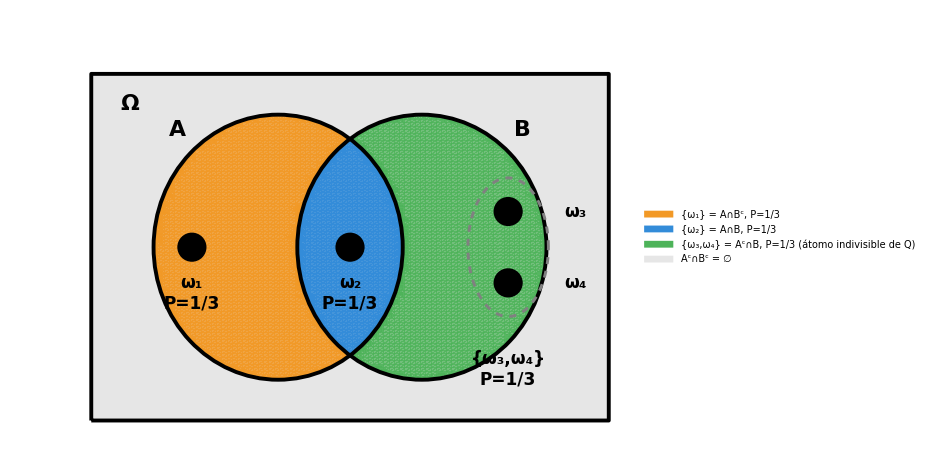

```mathematica
r=1.3;sep=0.75;
limX=2.7;limY=1.7;

(*Probabilidades resueltas del sistema P(ω1)=P(ω2)=P(B)/2,P(Ω)=1*)
p1=1/3;p2=1/3;p34=1/3;

colorA1=RGBColor[0.95,0.6,0.15];   (*{ω1}=A∩Bᶜ*)
colorA2=RGBColor[0.2,0.55,0.85];   (*{ω2}=A∩B*)
colorA3=RGBColor[0.3,0.7,0.35];    (*{ω3,ω4}=Aᶜ∩B*)
colorVacio=RGBColor[0.9,0.9,0.9];  (*Aᶜ∩Bᶜ=∅*)

grafico=Show[Graphics[{colorVacio,Rectangle[{-limX,-limY},{limX,limY}]}],RegionPlot[(x+sep)^2+y^2<r^2&&!((x-sep)^2+y^2<r^2),{x,-limX,limX},{y,-limY,limY},PlotStyle->Directive[colorA1,Opacity[0.85]],BoundaryStyle->None,PlotPoints->100,MaxRecursion->3],RegionPlot[(x+sep)^2+y^2<r^2&&(x-sep)^2+y^2<r^2,{x,-limX,limX},{y,-limY,limY},PlotStyle->Directive[colorA2,Opacity[0.9]],BoundaryStyle->None,PlotPoints->100,MaxRecursion->3],RegionPlot[!((x+sep)^2+y^2<r^2)&&(x-sep)^2+y^2<r^2,{x,-limX,limX},{y,-limY,limY},PlotStyle->Directive[colorA3,Opacity[0.75]],BoundaryStyle->None,PlotPoints->100,MaxRecursion->3],Graphics[{FaceForm[None],EdgeForm[{Black,Thickness[0.004]}],Rectangle[{-limX,-limY},{limX,limY}],Black,Thickness[0.004],Circle[{-sep,0},r],Circle[{sep,0},r],Text[Style["A",22,Bold],{-sep-r+0.25,r-0.15}],Text[Style["B",22,Bold],{sep+r-0.25,r-0.15}],Text[Style["Ω",22,Bold],{-limX+0.4,limY-0.3}],PointSize[0.03],Black,Point[{-sep-0.9,0}],Point[{0,0}],Point[{sep+0.9,0.35}],Point[{sep+0.9,-0.35}],Dashed,Gray,Thickness[0.003],Circle[{sep+0.9,0},{0.42,0.68}],Black,Text[Style["ω₁\nP=1/3",17,Bold],{-sep-0.9,-0.45}],Text[Style["ω₂\nP=1/3",17,Bold],{0,-0.45}],Text[Style["ω₃",17,Bold],{sep+1.6,0.35}],Text[Style["ω₄",17,Bold],{sep+1.6,-0.35}],Text[Style["{ω₃,ω₄}\nP=1/3",17,Bold],{sep+0.9,-1.2}]}],PlotRange->{{-limX-0.1,limX+0.1},{-limY-0.1,limY+0.3}},AspectRatio->Automatic,ImageSize->700];

imagenFinal=Legended[grafico,SwatchLegend[{colorA1,colorA2,colorA3,colorVacio},{"{ω₁} = A∩Bᶜ,  P=1/3","{ω₂} = A∩B,  P=1/3","{ω₃,ω₄} = Aᶜ∩B,  P=1/3  (átomo indivisible de Q)","Aᶜ∩Bᶜ = ∅"},LabelStyle->Directive[FontSize->17],LegendMarkerSize->22]];

imagenFinal
```

```mathematica
Export["prob_quesada_2_7_a.png",imagenFinal,Background->None,ImageResolution->600];
```